# EccGWs_Akhil

```mathematica
m1=30*1.98*10^30;m2=30*1.98*10^30;
G=6.67*10^-11;c=3*10^8;
```

### Analytical Plot of how Orbital Period evolves with eccentricity

```mathematica
Subscript[c, 0]=0.55;
```

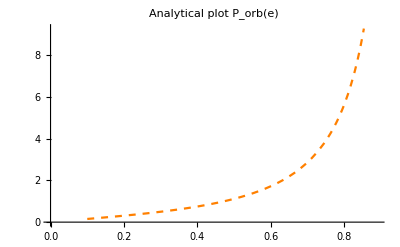

```mathematica
s1=Plot[(1/Subscript[c, 0] e^2/((1-e^2)^(19/6))(1+121/304 e^2)^(145/121))^(9/19),{e,0.1,0.89},PlotLabel->"Analytical plot P_orb(e)",PlotRange->Automatic,PlotStyle->{Orange,Dashed}]
```

```mathematica
(1/Subscript[c, 0] e^2/((1-e^2)^(19/6))(1+121/304 e^2)^(145/121))^(9/19)/.e-> 0.3
```

0.922631

Plot of semi - major axis

```mathematica
(*a[e]=(P[e^2]G(Subscript[m, 1]+Subscript[m, 2])/(4 π^2))^(1/3)*)
```

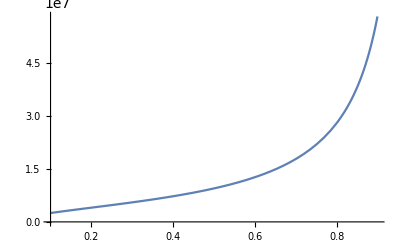

```mathematica
Plot[((1/Subscript[c, 0] e^2/((1-e^2)^(19/6))(1+121/304 e^2)^(145/121))^(18/19)(G(m1+m2))/(4 π^2))^(1/3),{e,0.1,0.9}]
```

### Numerical Plot of how Orbital Period evolves with eccentricity

```mathematica
sol1=NDSolve[{P'[e]==((-192π)/5((2π)/P[e])^(5/3)(1+73/24 e^2+37/96 e^4)(1-e^2)^(-7/2))/(-(608π)/15 e/P[e](1+121/304 e^2)(1-e^2)^(-5/2)),P[0.01]==0.3},P,{e,0.01,0.5},Method->Automatic]
```

{{P→InterpolatingFunction[…]}}

```mathematica
P[0.3]/.sol1
```

{17.7399}

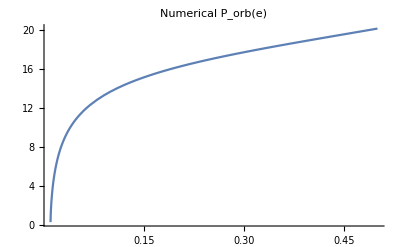

```mathematica
Plot[Evaluate[P[e]/.sol1],{e,0.01,0.5},PlotRange->All,PlotLabel->"Numerical P_orb(e)"]
```

### Numerical Plot_using EccGWS original

```mathematica
(*e'[t]==-(608π)/(15 c^5)e[t]/P[t](m1*m2)/(m1+m2)^(1/3)(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2)*)
```

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
sol=NDSolve[{P'[t]==(-192π)/(5 c^5)((2π G)/P[t])^(5/3)(m1*m2)/(m1+m2)^(1/3)(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==-(608π)/(15 c^5)(G^(5/3)*e[t])/P[t](m1*m2)/(m1+m2)^(1/3)(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),P[0]==0.3,e[0]==0.4},{P,e},{t,0,60}]
```

NDSolve::ndsz: At t == 6.57694, step size is effectively zero; singularity or stiff system suspected.

{{P→InterpolatingFunction[…],e→InterpolatingFunction[…]}}

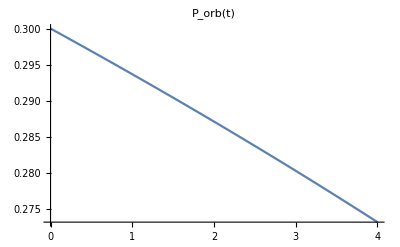

```mathematica
Plot[Evaluate[P[t]/.sol],{t,0,4},PlotRange->All,PlotLabel->"P_orb(t)"]
```

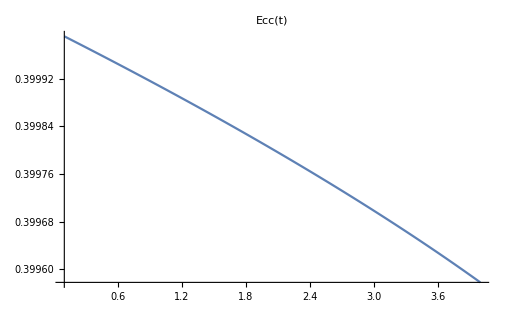

```mathematica
Plot[Evaluate[e[t]/.sol],{t,0.1,4},PlotRange->All,PlotLabel->"Ecc(t)"]
```

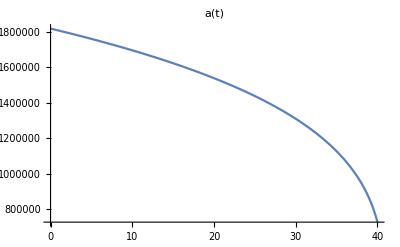

```mathematica
Plot[(P[t]^2*G(m1+m2)/(4 π^2))^(1/3)/.sol,{t,0,40},PlotLabel->"a(t)"]
```

#### Numerical Plot_using Zhang paper

```mathematica
m1=30*1.98*10^30;m2=30*1.98*10^30;
G=6.67*10^-11;c=3*10^8;μ=(m1*m1)/(m1+m2)
```

2.97×10^31

```mathematica
solM=NDSolve[{P'[t]==(-192π)/(5 c^5)((2π G(m1+m1))/P[t])^(5/3)μ/(m1+m2)(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==(-608π)/(15 c^5)((2π G(m1+m1))/P[t])^(5/3)(μ*e[t])/((m1+m2)*P[t])(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),P[0]==0.3,e[0]==0.4},{P,e},{t,0,60}]
```

NDSolve::ndsz: At t == 9.65468, step size is effectively zero; singularity or stiff system suspected.

{{P→InterpolatingFunction[…],e→InterpolatingFunction[…]}}

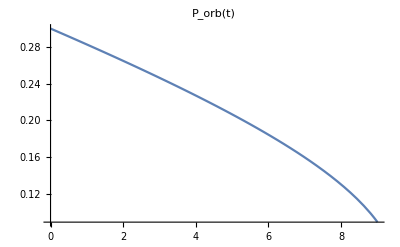

```mathematica
Plot[Evaluate[P[t]/.solM],{t,0,9},PlotRange->All,PlotLabel->"P_orb(t)"]
```

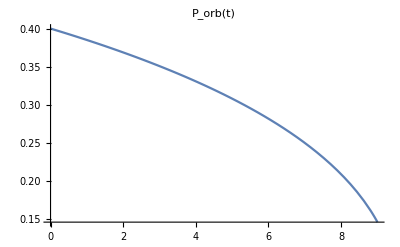

```mathematica
Plot[Evaluate[e[t]/.solM],{t,0,9},PlotRange->All,PlotLabel->"P_orb(t)"]
```

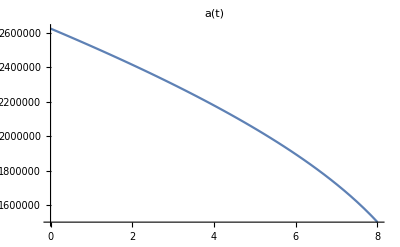

```mathematica
Plot[(P[t]^2*G(m1+m2)/(4 π^2))^(1/3)/.solM,{t,0,8},PlotLabel->"a(t)"]
```

#### Checking semi-major axis vs eccentricity

```mathematica
a0=(0.3^2*G/(4 π^2)*(m1+m2))^(1/3)
```

0.131612 (G (m1+m2))^(1/3)

```mathematica
m1=10*1.98*10^30;m2=10*1.98*10^30;G=6.67*10^-11;c=3*10^8;
```

```mathematica
solN=NDSolve[{a'[t]==-64/5 G^3/c^5(m1*m2*(m1+m2))/a[t]^3*(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==-304/15 G^3/c^5 e[t]/a[t]^4 m1*m2*(m1+m2)*(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),a[0]==a0,e[0]==0.4},{a,e},{t,0,60}]
```

{{a→InterpolatingFunction[…],e→InterpolatingFunction[…]}}

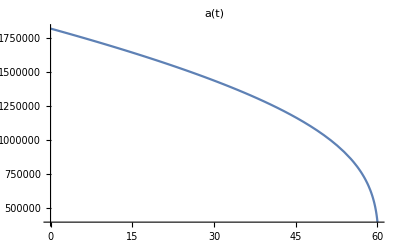

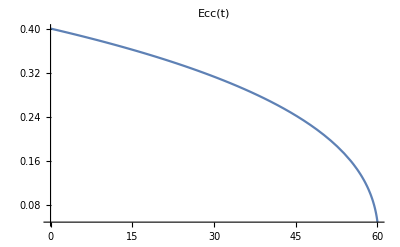

```mathematica
Plot[Evaluate[a[t]/.solN],{t,0,60},PlotRange->All,PlotLabel->"a(t)"]
Plot[Evaluate[e[t]/.solN],{t,0,60},PlotRange->All,PlotLabel->"Ecc(t)"]
```

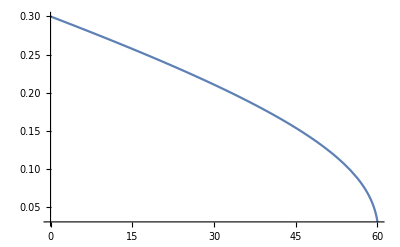

```mathematica
Plot[((a[t]^3*4 π^2)/(G(m1+m2)))^(1/2)/.solN,{t,0,60}]
```

```mathematica
solN1=NDSolve[{a'[e]==(-64/5 G^3/c^5(m1*m2*(m1+m2))/a[e]^3*(1+73/24 e^2+37/96 e^4)(1-e^2)^(-7/2))/(-304/15 G^3/c^5 e/a[e]^4 m1*m2*(m1+m2)*(1+121/304 e^2)(1-e^2)^(-5/2)),a[0.1]==a0},a,{e,0.1,0.89},Method->Automatic]
```

{{a→InterpolatingFunction[…]}}

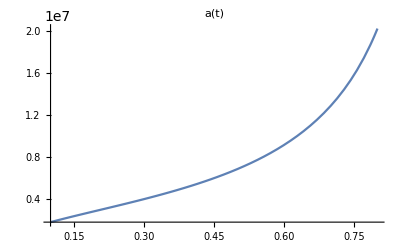

```mathematica
Plot[Evaluate[a[e]/.solN1],{e,0.1,0.8},PlotRange->All,PlotLabel->"a(t)"]
```

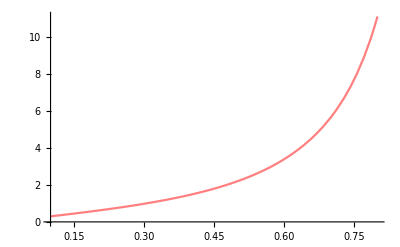

```mathematica
s2=Plot[((a[e]^3*4 π^2)/(G(m1+m2)))^(1/2)/.solN1,{e,0.1,0.8},PlotStyle->Pink]
```

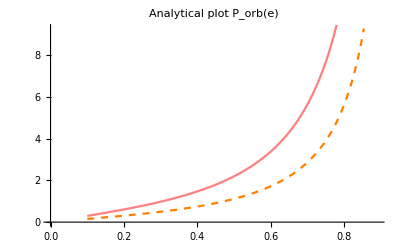

```mathematica
Show[s1,s2]
```

## Plotting Waveform_Miller formulas

```mathematica
Subscript[C, 0]=2/(1-Ene^2)-2a[t]
```

2/(1-Ene^2)-2 a[t]

```mathematica
Subscript[V, t]=(Ene*r^4)/(r^2-2r)
```

(Ene r^4)/(-2 r+r^2)

```mathematica
r=(a[t](1-e[t]^2))/(1+e[t]*Cos[ψ[t]])
```

(a[t] (1-e[t]^2))/(1+Cos[ψ[t]] e[t])

```mathematica
D[r,t]
```

((1-e[t]^2) a'[t])/(1+Cos[ψ[t]] e[t])-(2 a[t] e[t] e'[t])/(1+Cos[ψ[t]] e[t])-(a[t] (1-e[t]^2) (Cos[ψ[t]] e'[t]-e[t] Sin[ψ[t]] ψ'[t]))/(1+Cos[ψ[t]] e[t])^2

```mathematica
(*ψ'[t]=((1-Ene^2)^(1/2))/(Subscript[V, t](1-e^2))(a(1-e^2)-Subscript[C, 0](1-e)-e*a(1-e^2)-e*Subscript[C, 0](1-e)Cos[ψ])^(1/2)*(a(1-e^2)(1+e))^(1/2)*)
```

```mathematica
Mtot=20*1.98*10^30;m1=10*1.98*10^30;m2=10*1.98*10^30;G=6.67*10^-11;c=3*10^8;μ=(m1*m1)/(m1+m2)
```

9.9×10^30

```mathematica
Eorb[t]=-(G*m1*m2*μ)/(2a[t])
```

-(1.29438×10^83)/a[t]

```mathematica
Eorb0=-(G*m1*m2*μ)/(2a0)
```

-(1.29438×10^83)/a0

```mathematica
Ene[t]=1+Eorb[t]/μ
```

1-(1.30745×10^52)/a[t]

```mathematica
Ene0=1+Eorb0/μ
```

1-(1.30745×10^52)/a0

```mathematica
C0[t]=2/(1-Ene[t]^2)-2a[t]
```

2/(1-(1-(1.30745×10^52)/a[t])^2)-2 a[t]

```mathematica
r0=9.086*10^8;e0=0.3;P0=0.1
a0=(P0^2*G/(4 π^2)*(m1+m2))^(1/3);ϕinitial=0.1
```

0.1

0.1

```mathematica
ψ0=Cos[((a0(1-e0^2))/r0-1)/e0]^-1
```

-1.0181

```mathematica
(a0(1-e0^2))/(1+e0)
```

612235.

```mathematica
(*saving a'[t]=-64/5 G^3/c^5(m1*m2*(m1+m2))/a[t]^3*(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2))*) (*ϕ'[t]==(√(G*Mtot*μ*a[t](1-e[t]^2)))/((Ene[t]*r[t]^4)/(r[t]^2-2r[t]))*)
```

Initial radius = 1000 Megaparsecs

```mathematica
solE=NDSolve[{r'[t]==((1-e[t]^2) a'[t])/(1+Cos[ψ[t]] e[t])-(2 a[t] e[t] e'[t])/(1+Cos[ψ[t]] e[t])-(a[t] (1-e[t]^2) (Cos[ψ[t]] e'[t]-e[t] Sin[ψ[t]] ψ'[t]))/(1+Cos[ψ[t]] e[t])^2,ψ'[t]==((1-Ene[t]^2)^(1/2))/(((Ene[t]*r[t]^4)/(r[t]^2-2r[t]))(1-e[t]^2))(a[t](1-e[t]^2)-C0[t]*(1-e[t])-e[t]*a[t](1-e[t]^2)-e[t]*C0[t]*(1-e[t])Cos[ψ[t]])^(1/2)*(a[t](1-e[t]^2)(1+e[t]))^(1/2),ϕ'[t]==(√(G*Mtot*μ*a[t]*(1-e[t]^2)))/(μ*((Ene[t]*r[t]^4)/(r[t]^2-2r[t]))),a'[t]==-64/5 G^3/c^5(m1*m2*(m1+m2))/a[t]^3*(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==-304/15 G^3/c^5 e[t]/a[t]^4 m1*m2*(m1+m2)*(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),e[0]==e0,r[0]==r0,ψ[0]==ψ0, a[0]==a0,ϕ[0]==ϕinitial},{r,ψ,e,ϕ,a},{t,-1,0}]
```

{{r→InterpolatingFunction[…],ψ→InterpolatingFunction[…],e→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],a→InterpolatingFunction[…]}}

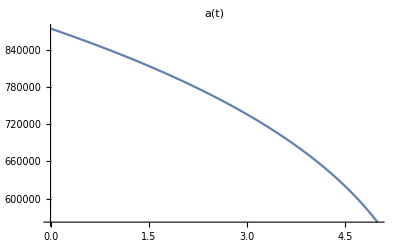

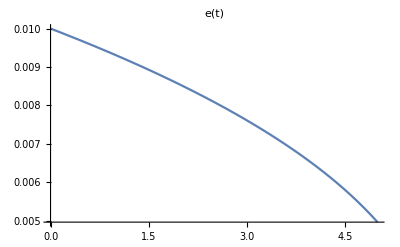

```mathematica
Plot[Evaluate[a[t]/.solE],{t,0,5},PlotRange->All,PlotLabel->"a(t)"]
Plot[Evaluate[e[t]/.solE],{t,0,5},PlotRange->All,PlotLabel->"e(t)"]
```

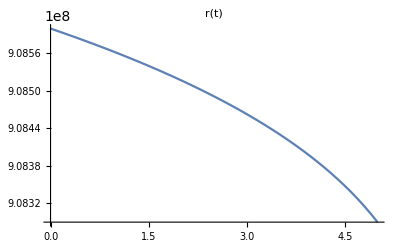

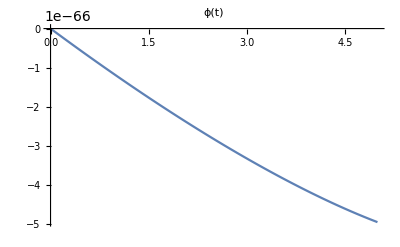

```mathematica
Plot[Evaluate[r[t]/.solE],{t,0,5},PlotRange->All,PlotLabel->"r(t)"]
Plot[Evaluate[ϕ[t]/.solE],{t,0,5},PlotRange->All,PlotLabel->"ϕ(t)"]
```

#### Angle ϕ describing where a body is in its orbital period

```mathematica
Eorb[t]=-(G*Mtot*μ)/(2a[t]);Lorb= √(G*Mtot*μ*a[t](1-e[t]^2));
```

```mathematica
Ene[t]=Eorb[t]/μ
```

-(1.32066×10^21)/a[t]

```mathematica
L=Lorb/μ;Subscript[V, t]=(Ene[t]*r[t]^4)/(r[t]^2-2r[t]);
```

```mathematica
(*ϕ'[t]=L/Subscript[V, t]*)
```

(0.000016334 √(a[t] (1-e[t]^2)) (-2 r[t]+r[t]^2))/((1-(1.32066×10^21)/a[t]) r[t]^4)

```mathematica
ϕinitial=(0.000016334013591276335 √(a0 (1-0.3^2)) (-2 r0+r0^2))/((1-(1.32066*^21)/a0)r0^4)
```

-3.04006×10^-62

```mathematica
θ=π/4;Dis=3.08257*10^23(*distance of GW150914*)
```

3.08257×10^23

```mathematica
Cos[2θ]
```

0

```mathematica
hplus[t]=μ/(2*Dis)((1-2Cos[2θ] Cos[ϕ[t]]^2-3Cos[2ϕ[t]])r'[t]^2+(3+Cos[2θ])(2Cos[2ϕ[t]] ϕ'[t]^2+Sin[2ϕ[t]]ϕ''[t])r[t]^2+(4(3+Cos[2θ])Sin[2ϕ[t]]ϕ'[t]r'[t]+(1-2Cos[2θ] Cos[ϕ[t]]^2-3Cos[2ϕ[t]])r''[t])r[t])
```

1.6058×10^7 ((1-3 Cos[2 ϕ[t]]) r'[t]^2+r[t] (12 Sin[2 ϕ[t]] r'[t] ϕ'[t]+(1-3 Cos[2 ϕ[t]]) r''[t])+3 r[t]^2 (2 Cos[2 ϕ[t]] ϕ'[t]^2+Sin[2 ϕ[t]] ϕ''[t]))

```mathematica
Plot[hplus[t]/.solE,{t,-1,0},PlotRange->Full]
```

-Graphics-

```mathematica
|
```

### Following peters

```mathematica
(*ψ[t]=((G(m1+m1)*a[t](1-e[t]^2))^(1/2))/r[t]^2*)
```

```mathematica
Mtot=20*1.98*10^30;m1=10*1.98*10^30;m2=10*1.98*10^30;G=6.67*10^-11;c=3*10^8;μ=(m1*m1)/(m1+m2)
```

9.9×10^30

```mathematica
r0=3.086*10^22;e0=0.5;P0=0.3
a0=(P0^2*G/(4 π^2)*(m1+m2))^(1/3);ϕinitial=0.0
```

0.3

0.

```mathematica
ψ0=((G(m1+m1)*a0(1-e0^2))^(1/2))/r0^2
```

1.77962×10^-32

```mathematica
Eorb[t]=-(G*m1*m2*μ)/(2a[t])
```

-(1.29438×10^83)/a[t]

```mathematica
Ene[t]=1+Eorb[t]/μ
```

1-(1.30745×10^52)/a[t]

```mathematica
D[ψ[t],t]
```

(2.56969×10^10 ((1-e[t]^2) a'[t]-2 a[t] e[t] e'[t]))/(√(a[t] (1-e[t]^2)) r[t]^2)-(1.02788×10^11 √(a[t] (1-e[t]^2)) r'[t])/r[t]^3

```mathematica
solP=NDSolve[{r'[t]==((1-e[t]^2) a'[t])/(1+Cos[ψ[t]] e[t])-(2 a[t] e[t] e'[t])/(1+Cos[ψ[t]] e[t])-(a[t] (1-e[t]^2) (Cos[ψ[t]] e'[t]-e[t] Sin[ψ[t]] ψ'[t]))/(1+Cos[ψ[t]] e[t])^2,ψ'[t]==(2.56968869709932*^10 ((1-e[t]^2) a'[t]-2 a[t] e[t] e'[t]))/(√(a[t] (1-e[t]^2)) r[t]^2)-(1.027875478839728*^11 √(a[t] (1-e[t]^2)) r'[t])/r[t]^3,ϕ'[t]==(√(G*Mtot*m1*m2))/((Ene[t]*r[t]^4)/(r[t]^2-2r[t])),a'[t]==-64/5 G^3/c^5(m1*m2*(m1+m2))/a[t]^3*(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==-304/15 G^3/c^5 e[t]/a[t]^4 m1*m2*(m1+m2)*(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),e[0]==e0,r[0]==r0,ψ[0]==ψ0, a[0]==a0,ϕ[0]==1},{r,ψ,e,ϕ,a},{t,0,10}]
```

NDSolve::underdet: There are more dependent variables, {a[t],e[t],Ene[t],r[t],ϕ[t],ψ[t]}, than equations, so the system is underdetermined.

NDSolve[{r'[t]==((1-e[t]^2) a'[t])/(1+Cos[ψ[t]] e[t])-(2 a[t] e[t] e'[t])/(1+Cos[ψ[t]] e[t])-(a[t] (1-e[t]^2) (Cos[ψ[t]] e'[t]-e[t] Sin[ψ[t]] ψ'[t]))/(1+Cos[ψ[t]] e[t])^2,ψ'[t]==(2.56969×10^10 ((1-e[t]^2) a'[t]-2 a[t] e[t] e'[t]))/(√(a[t] (1-e[t]^2)) r[t]^2)-(1.02788×10^11 √(a[t] (1-e[t]^2)) r'[t])/r[t]^3,ϕ'[t]==(5.9117×10^40 (-2 r[t]+r[t]^2))/(Ene[t] r[t]^4),a'[t]==-(8.18994×10^19 (1+(73 e[t]^2)/24+(37 e[t]^4)/96))/(a[t]^3 (1-e[t]^2)^(7/2)),e'[t]==-(1.29674×10^20 e[t] (1+(121 e[t]^2)/304))/(a[t]^4 (1-e[t]^2)^(5/2)),e[0]==0.5,r[0]==3.086×10^22,ψ[0]==1.77962×10^-32,a[0]==966641.,ϕ[0]==1},{r,ψ,e,ϕ,a},{t,0,10}]

-Graphics-

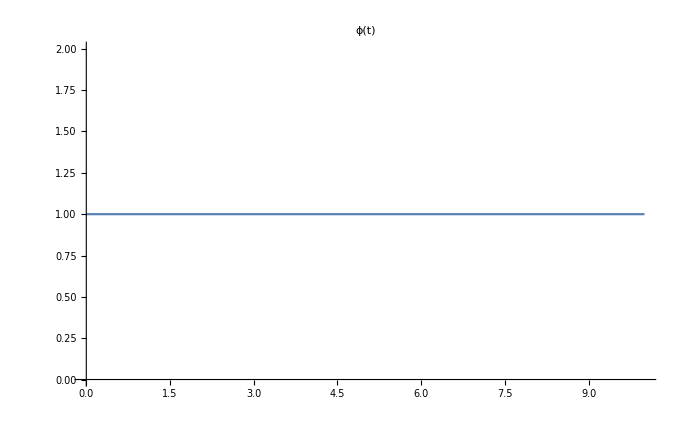

```mathematica
Plot[Evaluate[r[t]/.solP],{t,0,10},PlotRange->All,PlotLabel->"r(t)"]
Plot[Evaluate[ϕ[t]/.solP],{t,0,10},PlotRange->All,PlotLabel->"ϕ(t)"]
```

```mathematica
d= 3.08257*10^23;m1=2*1.98*10^30;m2=2*1.98*10^30;G=6.67*10^-11;c=3*10^8;
a= 10^8;
hcircular[t]=(2G(m1+m2))/(c^2*d)*(2G(m1+m2))/(c^2*a)Cos[ϕ[t]]
```

1.11765×10^-22 Cos[ϕ[t]]

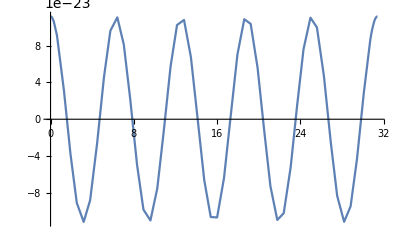

```mathematica
Plot[hcircular[t],{ϕ[t],0,10π}]
```

Ecc_Magiore

```mathematica
Mtot=4*1.98*10^30;m1=2*1.98*10^30;m2=2*1.98*10^30;G=6.67*10^-11;c=3*10^8;μ=(m1*m1)/(m1+m2);
```

```mathematica
r0=3.086*10^8;e0=0.1;P0=0.001
a0=(P0^2*G/(4 π^2)*(m1+m2))^(1/3)
```

0.001

21570.

```mathematica
ω0=(G*Mtot)/a0^3
```

3.94784×10^7

```mathematica
FindRoot[u==e0*Sin[u],{u,0}]
```

{u→0.}

```mathematica
N[(Cos[0]-e0)/(1-e0*Cos[0])]
```

1.

```mathematica
Solve[0==u-e0*Sin[u],u]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[0==u-0.1 Sin[u],u]

```mathematica
(*ψ0=((G(m1+m1)*a0(1-e0^2))^(1/2))/r0^2*) (*ψ'[t]==√((G*(m1+m2))/a[t]^3)(1-e[t]^2)^(-3/2)(1+e[t]Cos[ψ[t]])^2*)
```

```mathematica
ψ0=Cos[((a0(1-e0^2))/r0-1)/e0]^-1
```

-1.19126

```mathematica
solE=NDSolve[{r'[t]==((1-e[t]^2) a'[t])/(1+Cos[ψ[t]] e[t])-(2 a[t] e[t] e'[t])/(1+Cos[ψ[t]] e[t])-(a[t] (1-e[t]^2) (Cos[ψ[t]] e'[t]-e[t] Sin[ψ[t]] ψ'[t]))/(1+Cos[ψ[t]] e[t])^2,ψ'[t]==√((G*(m1+m2))/a[t]^3)(1-e[t]^2)^(-3/2)(1+e[t]Cos[ψ[t]])^2,a'[t]==-64/5 G^3/c^5(m1*m2*(m1+m2))/a[t]^3*(1+73/24 e[t]^2+37/96 e[t]^4)(1-e[t]^2)^(-7/2),e'[t]==-304/15 G^3/c^5 e[t]/a[t]^4 m1*m2*(m1+m2)*(1+121/304 e[t]^2)(1-e[t]^2)^(-5/2),e[0]==e0,r[0]==r0,ψ[0]==ψ0, a[0]==a0},{r,ψ,e,a},{t,-2,0}]
```

{{r→InterpolatingFunction[…],ψ→InterpolatingFunction[…],e→InterpolatingFunction[…],a→InterpolatingFunction[…]}}

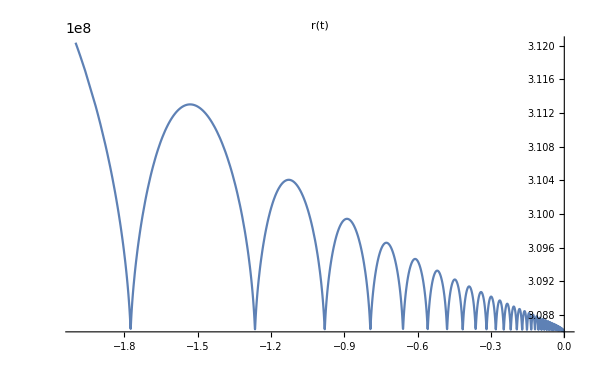

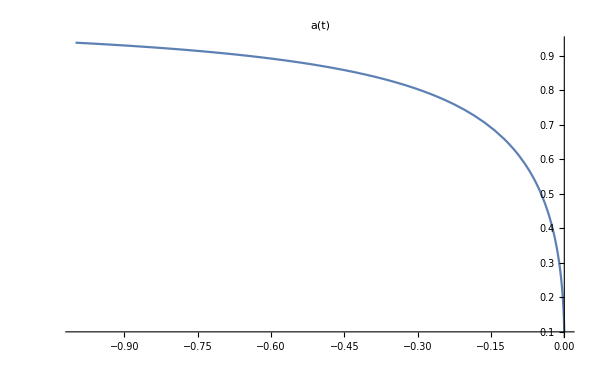

```mathematica
Plot[Evaluate[r[t]/.solE],{t,-2,0},PlotRange->All,PlotLabel->"r(t)",PlotRange->Full]
Plot[Evaluate[e[t]/.solE],{t,-1,0},PlotRange->All,PlotLabel->"a(t)"]
```

```mathematica
θ=π/4;Dis=3.08257*10^17(*distance of GW150914*)
```

3.08257×10^17

```mathematica
hplus[t]=(G*μ)/(c^4*2*Dis)((1-2Cos[2θ] Cos[ψ[t]]^2-3Cos[2ψ[t]])r'[t]^2+(3+Cos[2θ])(2Cos[2ψ[t]] ψ'[t]^2+Sin[2ψ[t]]ψ''[t])r[t]^2+(4(3+Cos[2θ])Sin[2ψ[t]]ψ'[t]r'[t]+(1-2Cos[2θ] Cos[ψ[t]]^2-3Cos[2ψ[t]])r''[t])r[t])
```

1.98346×10^-32 ((1-3 Cos[2 ψ[t]]) r'[t]^2+r[t] (12 Sin[2 ψ[t]] r'[t] ψ'[t]+(1-3 Cos[2 ψ[t]]) r''[t])+3 r[t]^2 (2 Cos[2 ψ[t]] ψ'[t]^2+Sin[2 ψ[t]] ψ''[t]))

```mathematica
hcross[t]=-(2*μ*Cos[θ]*G)/(Dis*c^4)(Sin[2ψ[t]] r'[t]^2+(Cos[2ψ[t]]ψ''[t]-2Sin[2ψ[t]] ψ'[t]^2)r[t]^2+(4Cos[2ψ[t]]ψ'[t]r'[t]+Sin[2ψ[t]]r''[t])r[t])
```

-5.61008×10^-32 (Sin[2 ψ[t]] r'[t]^2+r[t] (4 Cos[2 ψ[t]] r'[t] ψ'[t]+Sin[2 ψ[t]] r''[t])+r[t]^2 (-2 Sin[2 ψ[t]] ψ'[t]^2+Cos[2 ψ[t]] ψ''[t]))

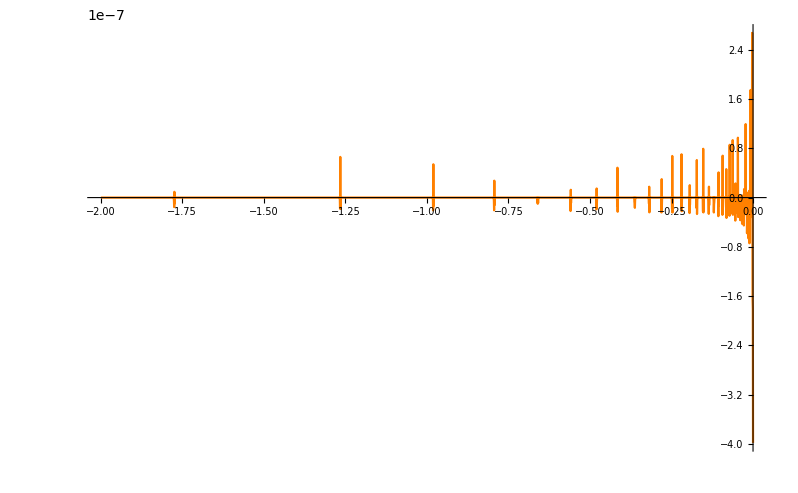

```mathematica
p1=Plot[hplus[t]/.solE,{t,-2,0},PlotRange->Full,PlotStyle->Orange]
```

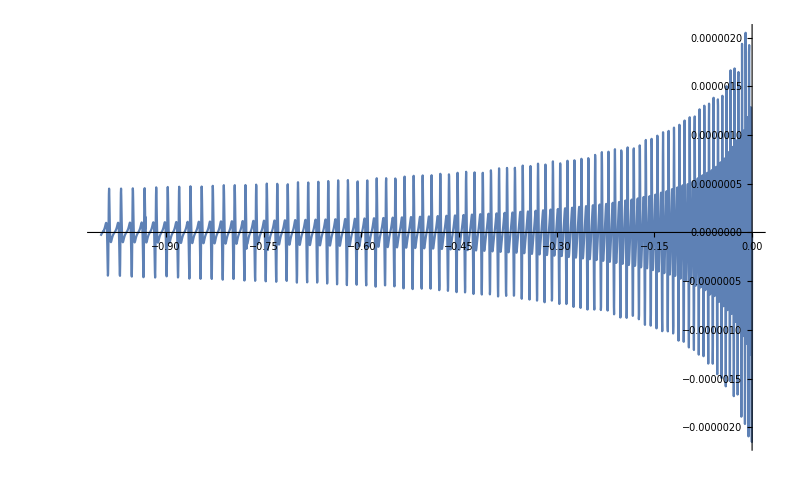

```mathematica
p2=Plot[hcross[t]/.solE,{t,-1,0},PlotRange->Full]
```

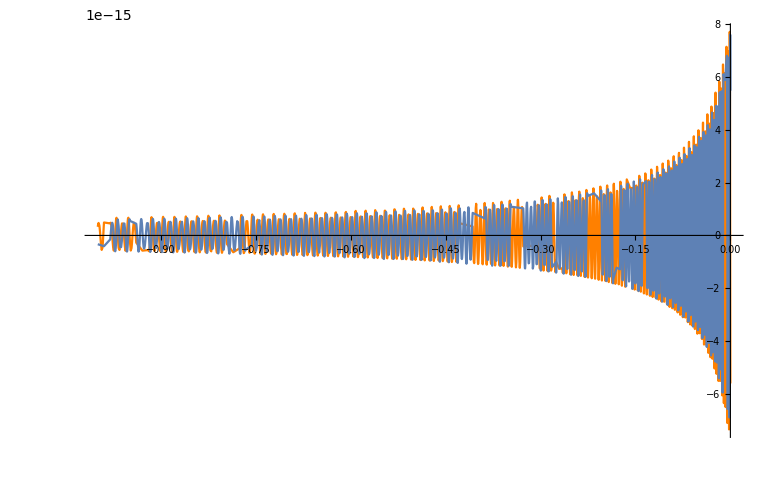

```mathematica
Show[p1,p2]
```

## h_+ of Gopal and Iyer

```mathematica
Mtot=3*1.98*10^30;m1=1.5*1.98*10^30;m2=1.5*1.98*10^30;G=6.67*10^-11;c=3*10^8;μ=(m1*m1)/(m1+m2);
η=μ/Mtot;
```

```mathematica
r0=3.086*10^10;e0=0.1;P0=0.001
a0=(P0^2*G/(4 π^2)*(m1+m2))^(1/3)
```

0.001

21570.

```mathematica
R=a0/(1-e0^2)
```

21787.9

```mathematica
C1=Cos[θ];S=Sin[θ]
```

1/(√2)

```mathematica
h[t]=(G*Mtot*η*C1)/(c^4*R)((1+C1^2)(((G*Mtot)/r[t]+r[t]^2 ψ'[t]^2-r'[t]^2)Cos[2ψ[t]]+2r'[t]r[t]ψ'[t]Sin[2ψ[t]])-S^2((G*Mtot)/r[t]-r[t]^2 ψ'[t]^2-r'[t]^2))
```

3.96859×10^-19 (1/2 (-(3.96198×10^20)/r[t]+r'[t]^2+r[t]^2 ψ'[t]^2)+3/2 (2 r[t] Sin[2 ψ[t]] r'[t] ψ'[t]+Cos[2 ψ[t]] ((3.96198×10^20)/r[t]-r'[t]^2+r[t]^2 ψ'[t]^2)))

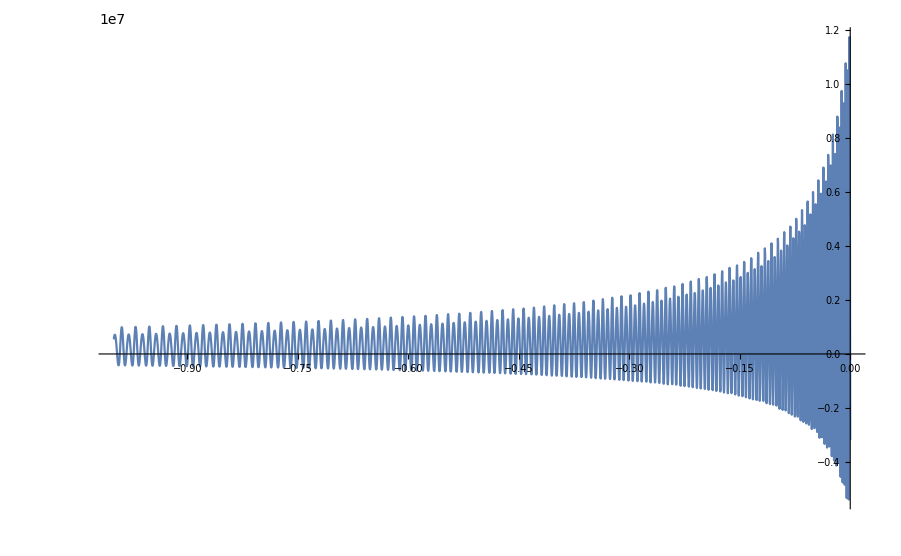

```mathematica
Plot[h[t]/.solE,{t,-1,0},PlotRange->All]
```